# Thesis Notebook

## 2D Orbit with the suns density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄) and r̄(r) functions

```mathematica
(*Block function says use this value of M then forget it*)

rofrbarOutside[rbar_] = Block[{M = 1}, rbar (1 + M/(2 rbar))^2]; 

rbarofrOutside[r_] = Block[{M = 1}, 1/2 (-M + r + Sqrt[r^2 - 2 M r])];
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] = Block[{M=1}, (1 + M/(2 rbar))^2];
α[rbar_] = Block[{M=1}, (1 - M/(2 rbar))/(1 + M/(2 rbar))];
```

Getting the value of the radius of the star in isotropic coordinates

```mathematica
rbarStar = rbarofrOutside[RStar] //  N
```

6.9641

## TOV Isotropic coords definitions

### Mass and Density functions from 2405.08113

#### Fixing the rho0 by letting the total mass integral equal to 1

```mathematica
rho[r_] := rho0(1 - r/R)^6;
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, R}]; (*Set equal to 1*)
```

```mathematica
rhoCentre[R_] := 63/(Pi R^3) (*From the above*)
rho0 = rhoCentre[RStar] //N;
```

```mathematica
MassFunc[r_] := Piecewise[{{252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3)) , r < RStar},
{M, r >= RStar}
}];
(*In 2405.08113 this function is divided by the solar mass, here I use M=1*)
```

### New density function

```mathematica
rho[r_] := Piecewise[{
{rho0(1 - r/RStar)^6, r < RStar},
{rho0, r >= RStar}
}];
```

### Getting new equations for the new interior metric:

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -Simplify[MassFunc[r]/r^2(rho[r] + Pressure)(1 + (4 Pi (Pressure) r^3)/MassFunc[r])(1 - (2 MassFunc[r])/r)^-1];
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := Simplify[MassFunc[r]/r^2(1 + (4 Pi (Pressure) r^3)/MassFunc[r])(1 - (2 MassFunc[r])/r)^-1];
```

#### Numerically Integrate these two partially coupled differential equations

```mathematica
rmin = 10^-17 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
ICs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
ICs},
{P, Phi},
{r, rmin, RStar}
][[1]] (*Very small rmin to avoid singularity sarp mentioned*)
```

{P→InterpolatingFunction[…],Phi→InterpolatingFunction[…]}

```mathematica
Pressure[r_] = P[r] /. sol1;
PhiMetric[r_] = Phi[r] /. sol1;

Pressure[RStar]
PhiMetric[RStar];
```

0.

#### Solving for the new r̄(r) and r(r̄) inside, obtaining r(r̄) via the interpolation trick Sarp explained

```mathematica
(*Defining the ODE*)
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

Numerically Integrating the above equation.

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, rmin, RStar}
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Generating the numerical data points:*)
(*Table[ expression, {variable, start, end, step}*)
data = Table[
{rbarofrInside[r], r}, (*Here Mathematica stores rbar[r] and r as a 2 element list - first entry is the independent variable and the one after is the dependent variable*)
{r, 0, RStar, (RStar - 0)/500} (*500 points*)
];
```

```mathematica
(*Evaluates ok at zero as sapr mentioned but integral doesn't like it one bit*)
```

```mathematica
(*Inverse Interpolation*)
rofrbarInside = Interpolation[data];(*Builds a function from the data passing through all points unlike Fit which approximately matches the data to a function I give it with parameters,  FindFit finds the parameters for me given I guess a suitable function*)
```

```mathematica
rofrbarInside[rbarStar];
```

### Putting this together to find the new interior metric functions

```mathematica
αInside[rbar_] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

```mathematica
αInside[rbarStar];
α[rbarStar];
```

```mathematica
AInside[rbar_] := rofrbarInside[rbar]/rbar;
```

```mathematica
A[rbarStar];
AInside[rbarStar];
```

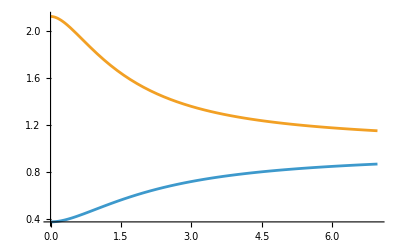

```mathematica
Plot[{αInside[rbar], AInside[rbar]}, {rbar, 0, rbarStar}]
```

### Sorting out the speed of sound as a function of r: a(r)

```mathematica
(*Getting the derivative of the density*)
rhodummy[r_] := rho0(1 - r/RStar)^6

drhodr[r_] := rhodummy'[r]
```

```mathematica
asos[r_] := (dPdr[r, Pressure[r]]/drhodr[r])^(1/2);
```

This is the a(r) function I will use for now:

```mathematica
asosPiecewise[r_] := Piecewise[
{
{asos[r], r <= RStar*.99989789203},
{asos[RStar*.99989789203], r >RStar*.99989789203}
}
];
asos[10^-120]; (*zero does not work but small r does!*)
```

```mathematica
asos[RStar*.99989789203] ;(*turns out to be nice cut off for the asos variable, could use this?*)
```

```mathematica
RStar*.99989789203;
```

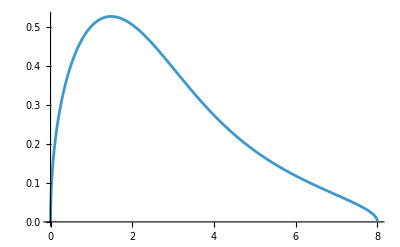

```mathematica
Plot[asosPiecewise[r], {r, 0, RStar}]
```

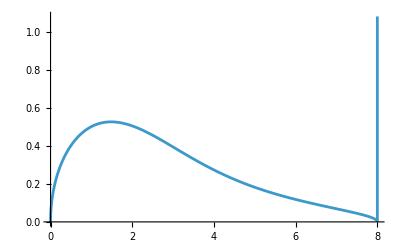

```mathematica
Plot[asos[r], {r, 0, RStar}]
```

#### Gets very messy from here downwards: doing it the Taylor expansion way

```mathematica
(*Limit[asos[r], r-> RStar] //  N (*goes to infinity when I sub in*);

Limit[
FullSimplify[
Series[asos[r], {r, RStar, 5}],
r>0
],
r-> RStar
]; *)
```

The above complex infinity is the issue discussed with Sarp, must Taylor expand.

```mathematica
Pdoubleprime[r_] := D[dPdr[x, Pressure[x]], x] /. x->r  (*Must use D as ' only differentiates wrt. the first argument*)
```

```mathematica
asosprimenearRStar[r_] := 1/(2 √asos[r])(Pdoubleprime[r]/drhodr[r] - dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r])
asosprimenearRStar[7.974] // N;
```

```mathematica
epsilon = 0.026; (*from RStar - 7.974 which is oscillating only in the 1e-4 range for alphaprime which is very small*)
```

```mathematica
asosprimenearRStar[7.974]*epsilon (*could either use this?*)
```

-0.000476814

Attempting to double differentiate and see where the function hits zero to find the max and minimum value of a’ in order to find the value of r to make a(r) a minimum

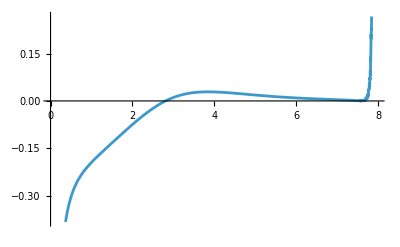

```mathematica
Plot[asosprimenearRStar'[r], {r, 0, 7.984}]
```

```mathematica
func[r_] := Pdoubleprime[r]/drhodr[r] - dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r]
func[.999*RStar];
```

```mathematica
Pdoubleprime[RStar*.999]/drhodr[RStar*.999];
```

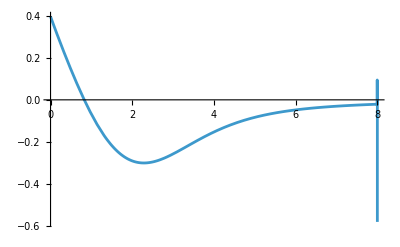

```mathematica
Plot[Pdoubleprime[r]/drhodr[r], {r, 0, RStar}]
```

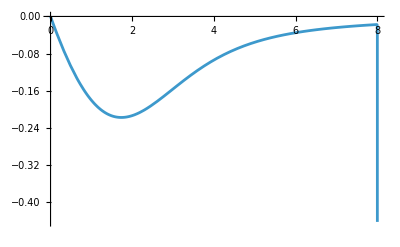

```mathematica
Plot[dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r], {r, 0, RStar}]
```

#### Speed of sound in isotropic coordinates

```mathematica
sosStarBoundary = rbarofrInside[RStar*.99989789203];
rbarStar;
Abs[sosStarBoundary-rbarStar]; (*Very close*)
```

```mathematica
asosPiecewise[rbar_] := Piecewise[
{
{10^-6, rbar <10^-20},
{asos[rofrbarInside[rbar]], rbar <= sosStarBoundary},
{asos[rofrbarInside[sosStarBoundary]], sosStarBoundary< rbar < rbarStar},
{10^-6, rbar > rbarStar}
}
];
asosPiecewise[sosStarBoundary];
asosPiecewise[8];
```

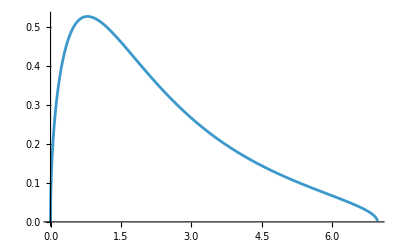

```mathematica
Plot[asosPiecewise[rbar], {rbar, 0, rbarStar}]
```

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar] //N;
```

```mathematica
rho[rbar_] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar <= rbarStar},
{0, rbar > rbarStar}
}
];

IsotropicCoordsPressure[rbar_] := Piecewise[
{
{Pressure[rofrbarInside[rbar]], rbar <= rbarStar},
{0, rbar > rbarStar}
}
]; (*Defined above*)
IsotropicCoordsPressure[0];
```

```mathematica
rho[0]
```

0.039167

## Setting up 2D ODEs for new density profile:

Constants that are going to be used

```mathematica
m = 10^-6; (*mass of PBH?*)
λGR[rbar_] := 1.49*asosPiecewise[rbar]
q = 2;
```

### Mach number interpolation

```mathematica
IVariable[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 1},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1}
}];
(*Approximate Log[Λ] ~ 10 following other authors [9] on 2404]*)
```

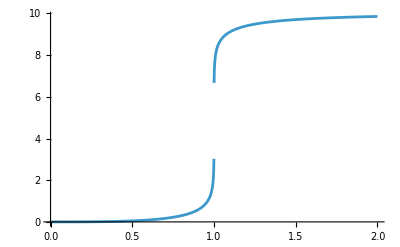

```mathematica
Plot[IVariable[Mach], {Mach, 0, 2},
PlotRange->All, Exclusions-> {Mach==1}]
```

#### Interpolating

```mathematica
x1 = 1;
x2 = 1;
y1 = 3.03;
y2 = 6.67;

anaylticline[Μach_] := y1 + (y2 - y1) (x - x1)/(x2 - x1);
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.9999},
{anaylticline[Μach], 0.9999 < Μach  < 1.0001},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.0001}
}];
```

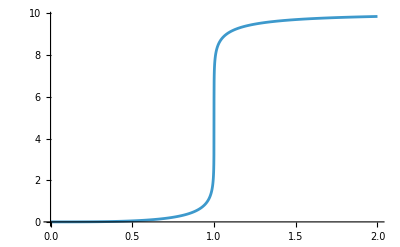

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, PlotRange->All, Exclusions->None]
```

#### Outside Star

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];

drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;

durdt2DOutside[rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur, uphi]((Derivative[1][A][rbar])/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + (Derivative[1][A][rbar])/(rbar^2*A[rbar]^3));
```

#### Inside Star

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagphi[rbar_, ur_, uphi_] := Piecewise[
{
{(√(ur^2+(uphi/rbar)^2))/AInside[rbar], rbar <rbarStar},
{(√(ur^2+(uphi/rbar)^2))/A[rbar], rbar >= rbarStar}
}
];(*paper eqn ut and umagphi*)

drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;

(*Mach stuff*)

Mach[rbar_, ur_, uphi_] := Piecewise[{
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar]  α[rbar] Ut[rbar, ur, uphi]), rbar < rbarStar},
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi]), rbar >= rbarStar}
}]

(*Accretion stuff*)

(* for Γ = 2 accretion rate*) (*This is my dmdt equation*)

mdot[m_, rbar_, ur_, uphi_] := 1.49* (4Pi rho[rbar] m^2)/(asosPiecewise[rbar]^2 + (umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2);


dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] λGR[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2)/asosPiecewise[rbar]^3)(asosPiecewise[rbar]^2/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] λGR[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2)/asosPiecewise[rbar]^3)(asosPiecewise[rbar]^2/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)uphi


dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagphi[rbar, ur, uphi]^3(-4π αInside[rbar]*(rho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagphi[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtdragphi[m, rbar, ur, uphi] + dpdtaccretionphi[m, rbar, ur, uphi]);

dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagphi[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagphi[rbar, ur, uphi]^3;

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur, uphi]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + (Derivative[1][AInside][rbar])/(rbar^2 AInside[rbar]^3)) +  η/m(dpdtdragr[m, rbar, ur, uphi]+ dpdtaccretionr[m, rbar, ur, uphi]);
```

Defining Mach number business

```mathematica
Μ[rbar_, ur_, uphi_] := Piecewise[{
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar] α[rbar] Ut[rbar, ur, uphi]), rbar > rbarStar},
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi]), rbar <= rbarStar}
}]
```

#### Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

Speed up factor

```mathematica
η= 100; (*Speed up parameter 72.5 is nice*)
```

Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
t0=0;
tEnd=2000;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[0]== rbar0,
ur[0]==0,
phi[0]==0,
uphi[0]==AngularMomentumUphi0,
mass[0] == m,

WhenEvent[rbar[t] <= 10^-3 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->20000
][[1]];
```

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Max::nord: Invalid comparison with ComplexInfinity attempted.

NDSolve::nrnum1: The function value ComplexInfinity is not a real number when the arguments are {160.867,6.9641,-0.0936921,3.44645,3.8236,1.×10^-6,-1,-1,1,1,0,1,1,1,-1,1}.

Max::nord: Invalid comparison with ComplexInfinity attempted.

NDSolve::nrnum1: The function value ComplexInfinity is not a real number when the arguments are {160.867,6.9641,-0.0936921,3.44645,3.8236,1.×10^-6,-1,-1,1,1,1,1,1,1,-1,1}.

NDSolve::nlnum: The function value $Failed is not a list of numbers with dimensions {5} at {t,rbar[t],ur[t],phi[t],uphi[t],mass[t],NDSolve`s$11249[t],NDSolve`s$11265[t],NDSolve`s$11487[t],NDSolve`s$11268[t],NDSolve`s$11248[t],NDSolve`s$11277[t],NDSolve`s$11278[t],NDSolve`s$11276[t],NDSolve`s$11488[t],NDSolve`s$11486[t]} = {160.867,{6.9641,-0.0936921,3.44645,3.8236,1.×10^-6},{-1,-1,1,1,1,1,1,1,-1,1}}.

```mathematica
rbar0
```

15.6507

“u” causing problems as velocities go to zero.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

160.867

160.867

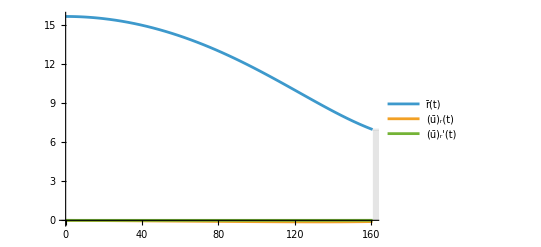

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

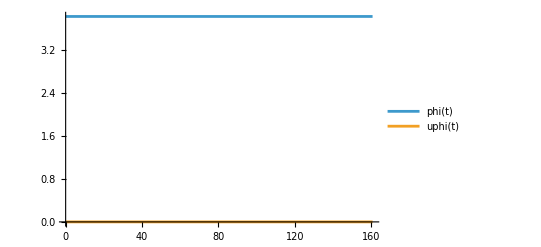

```mathematica
outFigAngular=Plot[{uphiNumIn[t],uphiNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

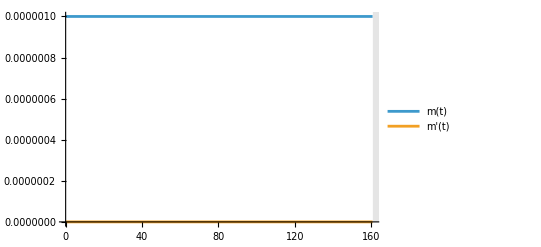

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

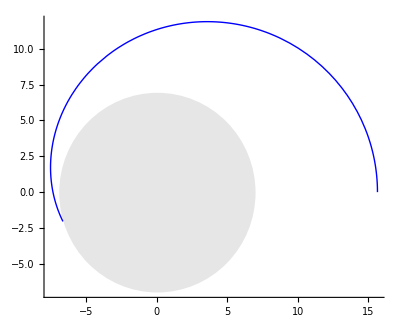

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

eccentric orbit and dig thru literature for u cubed and input speed factor.

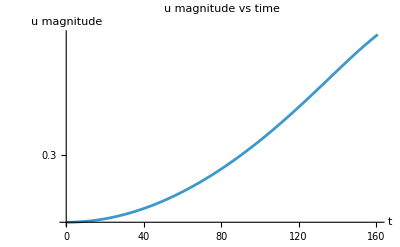

```mathematica
LogPlot[Evaluate[umagphi[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
(*Show me the value of u at tfinish*)
umagphi[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn;
```

#### Converting back to the areal radius to see the graphs and if it is different

```mathematica
(*Areal radius as a function of isotropic radius*)rFromRbar[rbar_]:=Piecewise[{{A[rbar]*rbar,rbar>=rbarStar},(*exterior*){AInside[rbar]*rbar,rbar<rbarStar}    (*interior*)}];

(*Areal radius along the orbit*)
arealr[t_]:=rFromRbar[rbarNumIn[t]];
```

```mathematica
x[t_]:=arealr[t] Cos[phiNumIn[t]];
y[t_]:=arealr[t] Sin[phiNumIn[t]];
```

```mathematica
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->1,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
```

```mathematica
(*Areal radius of the stellar surface*)
rstarAreal=A[rbarStar] rbarStar;

centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rstarAreal]}];
```

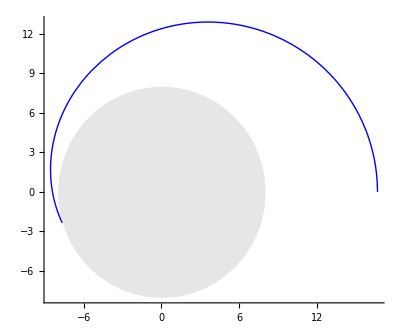

```mathematica
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

discontinuity here at the edge, not sure why?

## Capturing the PBH from infinity

Assuming PBH comes from infinity and just hits in and enters the star

#### Approaching the problem differently, using Keplerian orbits on the outside of the star and then GR on the inside to reduce the stiffness of the problem causing the error in the solver.

Setting v_inf to something physical is essential, most dark matter comes from the galactic halo, where things move at roughly 200km/s so with setting c = 1, vinf should be 10^-3 which implies the Energy at infinity should be approximately equal to 1 and very little energy loss is needed to bound the orbit.

#### Defining Initial Data Functions

```mathematica
vinf = 10^-3;
```

```mathematica
InitialEnergyAtInfinity[vinf_] := 1/(√(1 - vinf^2)); (*eq47 2404 paper*)
```

```mathematica
(*general formula for the magnitude of the velocity, for a general spherically symmetric Isotropic metric*)
umagVel[ur_, uphi_, rbar_] := √(ur^2 + (uphi/rbar)^2)
umagE[Energy_, rbar_] := A[rbar] √((Energy/α[rbar])^2 - 1); (*eq 48 in paper*)
```

```mathematica
(*Defining the Impact angle, which is the angle between the radial vector and the PBH's velocity vector*) (*It is the angle the PBH enters the star*)

urInit[psi_, Einit_] := -umagE[Einit , rbarStar]Cos[psi];
uphiInit[psi_, rbarStar_, Einit_] := rbarStar umagE[Einit ]Sin[psi]; (*Is defining angular momentum, L is equal to this*)
```

#### Setting the Initial conditions

```mathematica
(*we start at rbarStar*)
phi0 = 0;
Einf = InitialEnergyAtInfinity[vinf];
 u = umagE[Einf, rbarStar];
ImpactAngle = Pi/4; (*In radians, measured from center of star to the position of particle, in unit circle fashion, pi/2 corresponds to grazing the star as it enters and 0 corresponds to a radial drop*)
ur0 = -u*Cos[ImpactAngle];
uphi0 = (rbarStar)(u) Sin[ImpactAngle];
```

#### Sanity Check to see if the two energy formulas match up

```mathematica
Einf = InitialEnergyAtInfinity[vinf] //N
α[rbarStar]^2  Ut[rbarStar, ur0, uphi0] //N (*This Ut was upper indexed*)
```

1.

1.

#### Performing the inside integration

```mathematica
t0=0;
tEnd=10000;

solIn=NDSolve[
{
rbar'[t]==
If[
rbar[t] >=rbarStar,
drBardt[rbar[t],ur[t],uphi[t]],
drBardtInside[rbar[t],ur[t],uphi[t]]
],
ur'[t]==
If[
rbar[t] >=rbarStar,
durdt2DOutside[rbar[t],ur[t],uphi[t]],durdt2DInside[rbar[t],ur[t],uphi[t]]
],
uphi'[t]==
If[
rbar[t] >= rbarStar,
0,
duphidtInside[rbar[t],ur[t],uphi[t]]
],
phi'[t]==
If[
rbar[t] >= rbarStar,
dphidtOutside[rbar[t],ur[t],uphi[t]],dphidtInside[rbar[t],ur[t],uphi[t]]
],
rbar[0]==rbarStar,
ur[0]==ur0,
uphi[0]==uphi0,
phi[0]==phi0,

WhenEvent[
rbar[t] - rbarStar >0 && ur[t] >0,
"StopIntegration"
] (*Stop Integration if the PBH exits the star again*)
},
{rbar,ur,uphi,phi},{t,t0,tEnd},

WorkingPrecision->40,
MaxSteps->20000, 
Method->{"StiffnessSwitching"}
][[1]];
```

NDSolve::precw: The precision of the differential equation ({{rbar'[t]==If[rbar[t]≥6.9641,drBardt[rbar[t],ur[t],uphi[t]],drBardtInside[rbar[t],ur[t],uphi[t]]],ur'[t]==If[rbar[t]≥6.9641,durdt2DOutside[rbar[t],ur[t],uphi[t]],durdt2DInside[rbar[t],ur[t],uphi[t]]],«4»,uphi[0]==3.26599,phi[0]==0},«3»,{«9»[«1»]}}) is less than WorkingPrecision (40.).

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0.

Notes for next meeting

- Went through papers using ctrl F and also put them through, couldnt see anything to help with 1/u^3
- added in the epsilon to fix the issue, worked and got to the centre, although abruptly, maybe I can just turn off the drag if it becomes less important or something
- looked at PBH coming from infinity and got that setup as in paper, although issue with singularity persisted